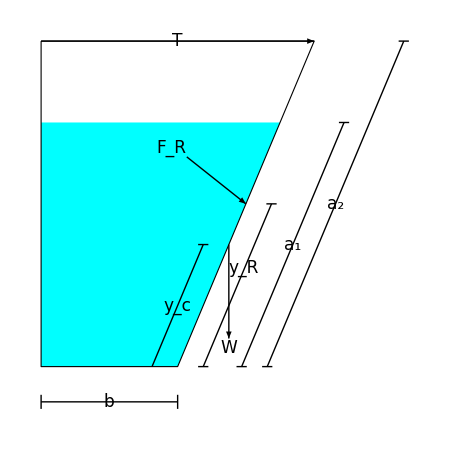
-Graphics- | y_c = a_1/2h_c = y_c sin θ

y_R = (I_(x c))/(y_c A) + y_ch_R = y_R sin θ

I_(x c) = 1/12 ba_1^3

A = a_1 b

```mathematica
Module[{θ,δA,δL,a1,a2,b,h1,h2,A,yc,hc,Ixc,yR,hR,xc1,xc2,p1,p2},
θ=60°;δA=2;δL=0.75;

a1=6;a2=8;b=4;
h1=a1*Sin[θ];h2=a2*Sin[θ];

A=a1*b;
yc=a1/2;hc=yc*Sin[θ];
Ixc=1/12*b*a1^3;yR=Ixc/(yc*A)+yc;hR=yR*Sin[θ];

xc1=x/.Quiet@Solve[hc==(h2-0)/(b+a2*Cos[θ]-b)*(x-b)+0,x][[1]];
xc2=x/.Quiet@Solve[hR==(h2-0)/(b+a2*Cos[θ]-b)*(x-b)+0,x][[1]];

p1=Graphics[{Thick,Arrowheads@0.065,
{FaceForm@Cyan,Polygon[{{0,h1},{0,0},{b,0},{b+h1/Sin[θ]*Cos[θ],h1}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,h2},{0,0},{b,0},{b+a2*Cos[θ],h2}}]},

{Arrowheads@{{-0.065,0.7},{0.065,0.3}},Arrow[{{0,h2},{b+a2*Cos[θ],h2}}]},
Text[Style[" T ",17,Italic,Background->White],{(b+a2*Cos[θ])/2,h2}],

Arrow[{{xc1,hc},{xc1,hc-δA}}],
Text[Style["W",17,Italic],{xc1,hc-δA},{0,1.2}],

Arrow[{{xc2+δA*Cos[90°+θ],hR+δA*Sin[90°+θ]},{xc2,hR}}],
Text[Style[Subscript[Style["F",Italic],"R"],17],{xc2+δA*Cos[90°+θ],hR+δA*Sin[90°+θ]},{1.1,-1.1}],

{Thin,
Line[{{b-δL,0},{xc1-δL,hc}}],Line[{xc1-#*δL,hc}&/@{0.8,1.2}],
Line[{{b+δL,0},{xc2+δL,hR}}],Line[{b+#*δL,0}&/@{0.8,1.2}],Line[{xc2+#*δL,hR}&/@{0.8,1.2}],

Line[{{0,-δL},{b,-δL}}],Line[{{#,-0.8*δL},{#,-1.2*δL}}]&/@{0,b},
Line[{{b+2.5*δL,0},{b+a1*Cos[θ]+2.5*δL,h1}}],Line[{b+2.5*δL+#*0.2*δL,0}&/@{-1,1}],Line[{b+a1*Cos[θ]+2.5*δL+#*0.2*δL,h1}&/@{-1,1}],
Line[{{b+3.5*δL,0},{b+a2*Cos[θ]+3.5*δL,h2}}],Line[{b+3.5*δL+#*0.2*δL,0}&/@{-1,1}],Line[{b+a2*Cos[θ]+3.5*δL+#*0.2*δL,h2}&/@{-1,1}]
},

Text[Style[Subscript[Style["y",Italic],"c"],17,Background->Cyan],{b+xc1-2*δL,hc}/2],
Text[Style[Subscript[Style["y",Italic],"R"],17,Background->White],{5.94,2.1}],

Text[Style[" b ",17,Italic,Background->White],{0.5*b,-δL}],
Text[Style[Subscript[Style["a",Italic],#1],17,Background->White],#2/2]&@@@{{1,{b+b+a1*Cos[θ]+5*δL,h1}},{2,{b+b+a2*Cos[θ]+7*δL,h2}}}
},ImageSize->{450,450}];

p2=Text@Style[Column[{
Row@{Subscript[Style["y",Italic],"c"]," = ",Subscript[Style["a",Italic],1],"/2",Spacer@20,
Subscript[Style["h",Italic],"c"]," = ",Subscript[Style["y",Italic],"c"]," sin ",Style["θ",Italic]},
Spacer@0,
Row@{Subscript[Style["y",Italic],"R"]," = ",Subscript[Style["I",Italic],Row@{Style["x",Italic]," c"}]/Row@{Subscript[Style["y",Italic],"c"],Style[" A",Italic]}," + ",Subscript[Style["y",Italic],"c"],Spacer@20,
Subscript[Style["h",Italic],"R"]," = ",Subscript[Style["y",Italic],"R"]," sin ",Style["θ",Italic]},
Spacer@0,
Row@{Subscript[Style["I",Italic],Row@{Style["x",Italic]," c"}]," = ",1/12,Style[" b",Italic],Subsuperscript[Style[" a",Italic],1,3]},
Spacer@0,
Row@{Style["A",Italic]," = ",Subscript[Style["a",Italic],1],Style[" b",Italic]}
}],17];

Grid@{{p1,p2}}
]
```

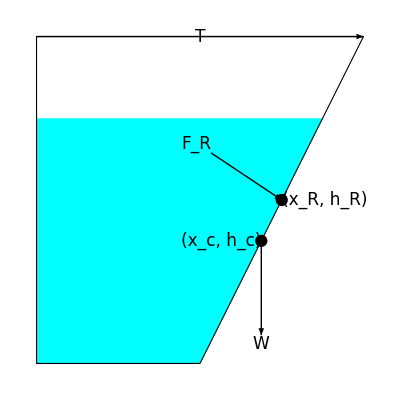

```mathematica
Module[{θ,δA,δL,a1,a2,b,h1,h2,A,yc,hc,Ixc,yR,hR,xc,xR},
θ=60°;δA=2;δL=0.75;

a1=6;a2=8;b=4;
h1=a1*Sin[θ];h2=a2*Sin[θ];

A=a1*b;
yc=a1/2;hc=yc*Sin[θ];
Ixc=1/12*b*a1^3;yR=Ixc/(yc*A)+yc;hR=yR*Sin[θ];

xc=x/.Quiet@Solve[hc==(h2-0)/(b+a2*Cos[θ]-b)*(x-b)+0,x][[1]];
xR=x/.Quiet@Solve[hR==(h2-0)/(b+a2*Cos[θ]-b)*(x-b)+0,x][[1]];

Graphics[{Thick,Arrowheads@0.065,
{FaceForm@Cyan,Polygon[{{0,h1},{0,0},{b,0},{b+h1/Sin[θ]*Cos[θ],h1}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,h2},{0,0},{b,0},{b+a2*Cos[θ],h2}}]},

{Arrowheads@{{-0.065,0.7},{0.065,0.3}},Arrow[{{0,h2},{b+a2*Cos[θ],h2}}]},
Text[Style[" T ",17,Italic,Background->White],{(b+a2*Cos[θ])/2,h2}],

Arrow[{{xc,hc},{xc,hc-δA}}],
Text[Style["W",17,Italic],{xc,hc-δA},{0,1.2}],

Arrow[{{xR+δA*Cos[90°+θ],hR+δA*Sin[90°+θ]},{xR,hR}}],
Text[Style[Subscript[Style["F",Italic],"R"],17],{xR+δA*Cos[90°+θ],hR+δA*Sin[90°+θ]},{1.1,-1.1}],

{PointSize@0.022,Point@{xc,hc},Point@{xR,hR}},

(*{Thin,
Line[{{0,-δL},{b,-δL}}],Line[{{#,-0.8*δL},{#,-1.2*δL}}]&/@{0,b},
Line[{{b+2.5*δL,0},{b+a1*Cos[θ]+2.5*δL,h1}}],Line[{b+2.5*δL+#*0.2*δL,0}&/@{-1,1}],Line[{b+a1*Cos[θ]+2.5*δL+#*0.2*δL,h1}&/@{-1,1}],
Line[{{b+3.5*δL,0},{b+a2*Cos[θ]+3.5*δL,h2}}],Line[{b+3.5*δL+#*0.2*δL,0}&/@{-1,1}],Line[{b+a2*Cos[θ]+3.5*δL+#*0.2*δL,h2}&/@{-1,1}]},*)

Text[Style[Row@{"(",Subscript[Style["x",Italic],"c"],", ",Subscript[Style["h",Italic],"c"],")"},17,Background->Cyan],{xc,hc},{1.2,0}],
Text[Style[Row@{"(",Subscript[Style["x",Italic],"R"],", ",Subscript[Style["h",Italic],"R"],")"},17,Background->White],{xR,hR},{-1.2,0}],

(*Text[Style[" b ",17,Italic,Background->White],{0.5*b,-δL}],
Text[Style[Subscript[Style["a",Italic],#1],17,Background->White],#2/2]&@@@{{1,{b+b+a1*Cos[θ]+5*δL,h1}},{2,{b+b+a2*Cos[θ]+7*δL,h2}}}*)
},ImageSize->{400,400}]
]
```